```mathematica
SetDirectory[NotebookDirectory[]]
```

U:\_Osebno\1. letnik\ROM\vaje7

```mathematica
"U:\\_Osebno\\1. letnik\\ROM\\vaje7"
```

U:\_Osebno\1. letnik\ROM\vaje7

```mathematica
tab =First[Import["rezultati.xlsx"]];
First[Import["rezultati.xlsx"]]
```

{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
Imena[podatki_]:= First[podatki]
```

```mathematica
Imena[tab]
```

{Priimek,Ime,Skupina,Točke}

```mathematica
Podatki[podatki_]:=Drop[podatki,1]
```

```mathematica
Podatki[tab]
```

{{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
IndeksStolpca[podatki_,stolpec_]:=Module[
{y},
y =Position[First[podatki],stolpec];
If[y=={},"Null",y]
]
```

```mathematica
IndeksStolpca[tab,"jovanka"]
```

Null

```mathematica
Stolpec[podatki_,stolpec_]:=Drop[First[Transpose[podatki][[First[IndeksStolpca[podatki,stolpec]]]]],1]
```

```mathematica
Stolpec[tab,"Ime"]
```

{Luka,Alenka,Petra,Andraž,Barbara,Mateja,Martin,Vesna,Valerija,Primož,Polona,Katarina,Janja,Aleš,Sabina,Katja,Jaka,Kristina,Grega,Tatjana,Primož,Matjaž,Igor,Matej,Aleksander,Mojca,Andreja,Tomaž}

```mathematica
PovprecjeTock[podatki_]:=Mean[Stolpec[podatki,"Točke"]]
```

```mathematica
PovprecjeTock[tab]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_,stolpec_]:=Union[Stolpec[podatki,stolpec]]
```

```mathematica
RazlicneVrednosti[tab,"Točke"]
```

{26.,30.,34.,36.,38.,39.,42.,43.,44.,46.,57.,58.,64.,66.,67.,70.,76.,77.,79.,85.,86.,90.,93.,94.,100.}

```mathematica
Vrstica[podatki_,i_]:=Podatki[podatki][[i]]
```

```mathematica
Vrstica[tab,1]
```

{Furlan,Luka,A,93.}

## 3. Naloga

```mathematica
meje={50,60,70,80,90}
```

{50,60,70,80,90}

```mathematica
OcenaZaMeje[{za6_,za7_,za8_,za9_,za10_},tocke_]:=Module[{x,y},
x={za6,za7,za8,za9,za10};
y=tocke;
If[y<za10,If[y<za9,If[y<za8,If[y<za7,If[y<za6,0,6],7],8],9],10]]
```

```mathematica
OcenaZaMeje[meje,49]
```

0

## 4. naloga

```mathematica
y={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FunkcijaOcen[ime_,podStolpec_]:=Join[podStolpec,ime]
```

```mathematica
DodajStolpec[podatki_,ime_,podStolpec_]:=Transpose[Join[Transpose[podatki],{FunkcijaOcen[podStolpec,{ime}]}]]
```

```mathematica
DodajStolpec[tab,"Ocene",y]//TableForm
```

Priimek | Ime | Skupina | Točke | Ocene
Furlan | Luka | A | 93. | 0
Karakaš | Alenka | A | 94. | 0
Kočar | Petra | B | 44. | 0
Kofol | Andraž | C | 34. | 0
Kumar | Barbara | B | 67. | 0
Logar | Mateja | A | 42. | 0
Pance | Martin | B | 64. | 0
Pleterski | Vesna | C | 30. | 0
Trček | Valerija | B | 70. | 0
Virant | Primož | C | 58. | 0
Vesel | Polona | C | 66. | 0
Žveglič | Katarina | A | 46. | 0
Cvelbar | Janja | B | 39. | 0
Furlan | Aleš | B | 36. | 0
Iskra | Sabina | A | 77. | 0
Jerman | Katja | B | 100. | 0
Karničar | Jaka | C | 26. | 0
Korošec | Kristina | B | 86. | 0
Kržišnik | Grega | B | 90. | 0
Obrenović | Tatjana | C | 44. | 0
Puncer | Primož | A | 57. | 0
Ribnikar | Matjaž | A | 43. | 0
Štemberger | Igor | B | 85. | 0
Šubašič | Matej | C | 76. | 0
Tekavčič | Aleksander | A | 34. | 0
Tratnik | Mojca | B | 79. | 0
Smrekar | Andreja | A | 38. | 0
Bezek | Tomaž | B | 38. | 0

### 5. naloga

```mathematica
Točke=Drop[Last[Transpose[tab]],1]
```

{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

```mathematica
IzracunajOcene[tocke_]:=OcenaZaMeje[meje,tocke]
```

```mathematica
pOcena = Map[IzracunajOcene,Točke]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
SteviloOcen[ocene_]:={BinCounts[pOcena,{0,11}][[1]],BinCounts[pOcena,{0,11}][[7]],BinCounts[pOcena,{0,11}][[8]],BinCounts[pOcena,{0,11}][[9]],BinCounts[pOcena,{0,11}][[10]],BinCounts[pOcena,{0,11}][[11]]}
```

```mathematica
PorazdelitevOcen = SteviloOcen[pOcena]
```

{13,2,3,4,2,4}

## 6. naloga

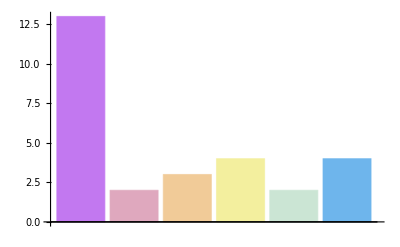

```mathematica
BarChart[PorazdelitevOcen,ChartStyle->"Pastel"]
```